```mathematica
SetDirectory[NotebookDirectory[]];
<<"helpers.wls"

$PlotTheme = "Default";
frameLabelStyle[text_]:= Style[text, FontSize->12,FontColor->Gray];
frameTicksStyle = Directive[FontSize-> 8, FontColor-> Gray];
legendStyle [text_]:= Style[text, FontSize->12, FontColor->Gray];
plotLabelStyle[text_]:= Style[text, FontSize->14, FontColor->Gray];
cm = 72/2.54;
colorMap = 97;

thesisImages = FileNameJoin[{NotebookDirectory[], "..", "..", "thesis","chapters","img"}];
```

## Find Simulation Parameters

### Find Intensity and Background

```mathematica
adjustParams[20, 5];
```

```mathematica
adjustParams[40, 5];
```

```mathematica
adjustParams[60, 5];
```

```mathematica
adjustParams[80, 5];
```

```mathematica
adjustParams[80, 10];
```

```mathematica
adjustParams[80, 15];
```

```mathematica
adjustParams[80, 20];
```

```mathematica
adjustParams[80, 25];
```

```mathematica
adjustParams[80, 30];
```

### Results

```mathematica
Needs["DatabaseLink`"];
```

```mathematica
<<"../classify-smi/helpers-scores.wls";
<<"../classify-smi/helpers-data.wls";
<<"../classify-smi/scores.wls";
```

```mathematica
conn = OpenSQLConnection[JDBC["PostgreSQL","127.0.0.1/teodor"],"Username"->"teodor"];
```

```mathematica
smi2014records = SmiUnpackRecords@@@SQLExecute[conn, "select 
source_data_set, 
source_track_id, 
track_start, 
track_end, 
category, 
levels_order, 
track_size,
frame_dim_int, 
frame_dim_img, 
scores, 
levels, 
data_int, 
data_img,
levels_old
from smidata
where 
    dataset_id = 13
and category = 1
order by source_data_set, source_track_id"
];
```

```mathematica
simIfB05 = <||>;
```

```mathematica
(simIfB05[#] = SmiUnpackRecords@@@SQLExecute[conn, "select 
source_data_set, 
source_track_id, 
track_start, 
track_end, 
category, 
levels_order, 
track_size,
frame_dim_int, 
frame_dim_img, 
scores, 
levels, 
data_int, 
data_img,
levels_old
from smidata
where 
    dataset_id = 37
and source_data_set like '%I_"<>numStr[#]<>"%fB_00005%g_250%'
order by source_data_set, source_track_id"] )&/@ Range[20, 80, 20];
```

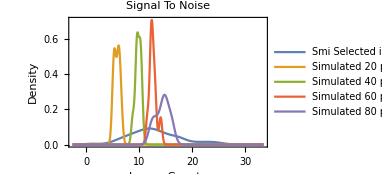

```mathematica
Block[{img},
img = SmoothHistogram[{
SignalToNoiseL1/@smi2014records,
SignalToNoiseL1/@simIfB05[20],
SignalToNoiseL1/@simIfB05[40],
SignalToNoiseL1/@simIfB05[60],
SignalToNoiseL1/@simIfB05[80]},
PlotLabel->plotLabelStyle["Signal To Noise"],
Frame-> True,
FrameTicksStyle->frameTicksStyle,
FrameLabel-> (frameLabelStyle/@{"Image Counts", "Density"}),
PlotLegends->(legendStyle/@{
"Smi Selected in 2014 L1",
"Simulated 20 photons",
"Simulated 40 photons",
"Simulated 60 photons",
"Simulated 80 photons"}),
ImageSize->10cm];
Export[FileNameJoin[{thesisImages, "methods-simulations-signal-to-noise.pdf"}], img];
img
]
```

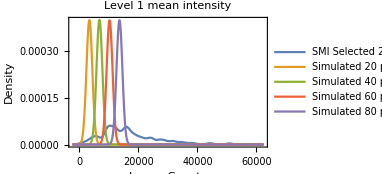

```mathematica
Block[{img},
img = SmoothHistogram[{
#[[scoresI]]["cts_mean_lvl_1"]&/@smi2014records,
#[[scoresI]]["cts_mean_lvl_1"]&/@simIfB05[20],
#[[scoresI]]["cts_mean_lvl_1"]&/@simIfB05[40],
#[[scoresI]]["cts_mean_lvl_1"]&/@simIfB05[60],
#[[scoresI]]["cts_mean_lvl_1"]&/@simIfB05[80]},
1000,
PlotLabel->plotLabelStyle["Level 1 mean intensity"],
Frame-> True,
FrameLabel-> (frameLabelStyle/@{"Image Counts", "Density"}),
FrameTicksStyle->frameTicksStyle,
PlotLegends->(legendStyle/@{"SMI Selected 2014",
"Simulated 20 photons",
"Simulated 40 photons",
"Simulated 60 photons",
"Simulated 80 photons"}),
PlotRange->All,
ImageSize->10cm];
Export[FileNameJoin[{thesisImages, "methods-simulations-l1-intensity.pdf"}],img];
img
]
```

```mathematica
simBfI80 = <||>;
```

```mathematica
(simBfI80[#] = SmiUnpackRecords@@@SQLExecute[conn, "select 
source_data_set, 
source_track_id, 
track_start, 
track_end, 
category, 
levels_order, 
track_size,
frame_dim_int, 
frame_dim_img, 
scores, 
levels, 
data_int, 
data_img,
levels_old
from smidata
where 
    dataset_id = 37
and source_data_set like '%I_00080%fB_"<> numStr[#]<>"-q_0_92-c_0_02-g_250-r_50-f_12_7-sigma_1_06157%'
order by source_data_set, source_track_id"] )&/@ Range[5, 30,5];
```

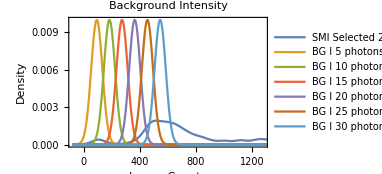

```mathematica
Block[{img},
img = SmoothHistogram[{
Mean/@smi2014records[[All,9,All, 6]],
Mean/@simBfI80[5][[All, 9, All, 6]],
Mean/@simBfI80[10][[All, 9, All, 6]],
Mean/@simBfI80[15][[All, 9, All, 6]],
Mean/@simBfI80[20][[All, 9, All, 6]],
Mean/@simBfI80[25][[All, 9, All, 6]],
Mean/@simBfI80[30][[All, 9, All, 6]]
}, 40,
Frame-> True,
FrameTicksStyle->frameTicksStyle,
FrameLabel->(frameLabelStyle/@{"Image Counts","Density"}),
PlotLabel->plotLabelStyle["Background Intensity"],
PlotLegends->(legendStyle/@{
"SMI Selected 2014",
"BG I 5 photons",
"BG I 10 photons",
"BG I 15 photons",
"BG I 20 photons",
"BG I 25 photons",
"BG I 30 photons"
}),
ImageSize->10cm];
Export[FileNameJoin[{thesisImages, "methods-simulations-background-int.pdf"}], img];
img
]
```

Based on the histogram of the level 1 signal to noise ratio and level 1 intensity the best value for the fluorophore intensity is 80 photons

Based on the histogram of the background intensity values the best value for the background is 30 photons

Both of these values are at gain 250, A/D factor of 12.7, quantum efficiency of 0.92, spurious charge of 0.02, and read out noise with standard deviation of 50.

## Classification of Single Molecule Data

### Analyzable Tracks

These tracks need to be analysed

#### Helper functions

#### Analyzable Tracks

Generate 3x3 analyzable tracks. Generate a data set with 100, 50, 20, and 10 frames per level. Note that not every track here is in the used class. Some tracks will be rejected by measure_levels2.

```mathematica
exportData[
NotebookDirectory[],
getDataName["an-batch_"<>numStr[#1],Length[#2], fI,fB],
#2
]&@@@ Transpose[{
Flatten@Table[{i, i}, {i, 71,80}],
addNoise[Quiet@generateAnalysable[fI, fB, {
100, 50,
100, 50,
100, 50,
100, 50,
100, 50,
100, 50,
100, 50,
100, 50,
100, 50,
100, 50
}, frameSize, 1]]
}];
```

### Non-Analyzable Tracks

Run the script simulate-na.wls <first_batch_id>

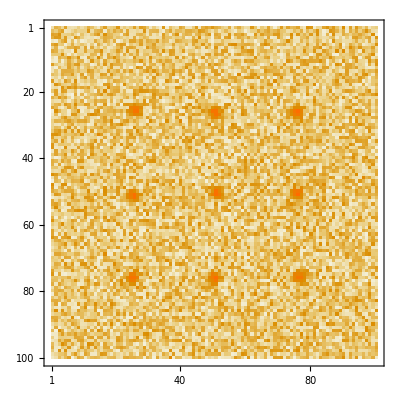

```mathematica
MatrixPlot[ndata[[155]]]
```

### Generate Beads

```mathematica
fI = 80;
fB = 30;
```

```mathematica
beads = addNoise@generateBeads[fI,fB, 5, frameSize];
```

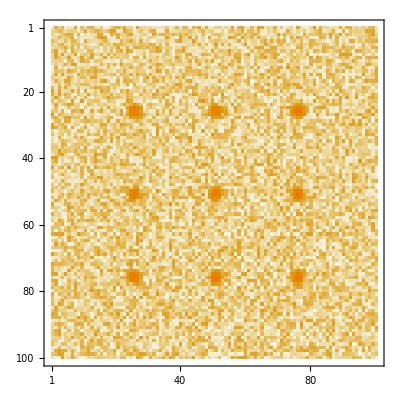

```mathematica
MatrixPlot[beads⟦1,5⟧]
```

```mathematica
exportBeads[FileNameJoin[{NotebookDirectory[],getDataName["beads-100x100", 5, fI, fB]}],beads⟦1⟧];
```

## Level Detection Algorithm

### Training Set

Take 20 samples of each type of data set. These are 60 tracks in total. Add to these tracks 9 with manually chosen level and run the level detection with these samples.

#### Level Changes with Equal Intensity

```mathematica
states = Table[
FluorophoresHMM[400, {{0.98, 0.018, 0.002}, {0.02, 0.98, 0}, {0, 0, 1}}],
 10];
```

```mathematica
ndata = addNoise@generateDataSet[states, 60,120,80];
```

```mathematica
exportSimulatedData["ld-mc-batch_", 41, ndata, states];
```

```mathematica
CloseKernels[];
```

#### Small Intensity Change.

```mathematica
states = Table[
FluorophoresHMM[400, {{0.98, 0.018, 0.002}, {0.02, 0.98, 0}, {0, 0, 1}}],
 10];
```

```mathematica
LaunchKernels[];
```

```mathematica
ndata = addNoise@generateDataSet[states, 30,80,80];
```

```mathematica
CloseKernels[];
```

```mathematica
exportSimulatedData["ld-mc-dim-batch_", 41, ndata, states];
```

#### Short Levels

```mathematica
states = Table[
FluorophoresHMM[400, {{0.92, 0.078, 0.002}, {0.08, 0.92, 0}, {0, 0, 1}}],
 10];
```

```mathematica
LaunchKernels[];
```

```mathematica
ndata = addNoise@generateDataSet[states, 60,120,80];
```

```mathematica
CloseKernels[];
```

```mathematica
exportSimulatedData["ld-mc-short-batch_",41, ndata, states];
```

#### Level Gap Higher Intensity

```mathematica
states = {
Join[Table[{1, 0}, 20], Table[{0, 1}, 3], Table[{0, 0}, 20], Table[{0, 1}, 3],Table[{1, 0}, 20], Table[{1, 1}, 3],Table[{0, 0}, 20],Table[{1, 1}, 3],Table[{1, 0}, 20],Table[{0, 0}, 20],Table[{1, 1}, 3],Table[{0, 1}, 3],Table[{0, 0}, 20],Table[{0, 1}, 3],Table[{1, 1}, 3],Table[{0, 0}, 20],Table[{0, 1}, 3],Table[{1, 0}, 20],Table[{1, 1}, 3],Table[{1, 0}, 20],Table[{0, 1}, 3],Table[{0, 0}, 20],Table[{0, 1}, 3],Table[{1, 0}, 3],Table[{1, 1}, 3],Table[{1, 0}, 3],Table[{0, 1}, 3],Table[{0, 0}, 3]
]
};
```

```mathematica
ndata = addNoise@generateDataSet[states, 120,60,80];
```

```mathematica
exportSimulatedData["ld-lvlgap-batch_", 1, ndata, states];
```

#### Level Gap Lower Intensity

```mathematica
states = {
Join[
Table[{1, 1}, 20],
Table[{0, 1}, 3],
Table[{1, 0}, 20],

Table[{0, 1}, 3],
Table[{0, 0}, 20],
Table[{0, 1}, 3],
Table[{1, 0}, 10],
Table[{0, 1}, 3],
Table[{1, 1}, 10],
Table[{0, 1}, 3],
Table[{1, 0}, 5],
Table[{0, 1}, 3],
Table[{0, 0}, 5]
]
};
```

```mathematica
ndata = addNoise@generateDataSet[states, 120,60,80];
```

```mathematica
exportSimulatedData["ld-lvlgapLI-batch_", 1, ndata, states];
```

### Test Cases

## Display Progress

```mathematica
showdata = {ndata};
```

```mathematica
coolcolor[value_, min_, max_]:= RGBColor[#, #, #]&@((value - min)/max);
index = 1;
min = Min@showdata;
max = Max@showdata;
Dynamic@MatrixPlot[showdata⟦1,index⟧,PlotRange->All, ColorFunctionScaling->False,
ColorFunction-> (coolcolor[#,min, max ]&)]
```

```mathematica
Slider[Dynamic[index],{1,Length[showdata[[1]]],1}]
```

```mathematica
cm = 72./2.54;
```

### Thesis images

```mathematica
frame = addNoise[{{GenerateFrame[Table[1, 9], 
Table[120, 9], Flatten[
Table[
{25*x,25*y},
{x, 1, 3}, {y, 1, 3}], 1],
30, 100]
}}];
```

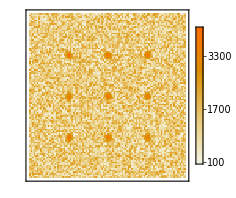

```mathematica
Block[{img},
img = MatrixPlot[First@First@frame,
FrameTicks-> None,
PlotRange->All,
PlotLegends->Automatic,
ImageSize->7cm];
Export[FileNameJoin[{thesisImages,"methods-simulations-typical-frame.pdf"}], img];
img]
```

```mathematica
frameSingleFluorophore = GenerateFrame[{1}, {100},{{9.5, 9.5}}, 30, 20];
```

```mathematica
nframeSingleFluorophore  = First@First@addNoise[{{frameSingleFluorophore }}];
```

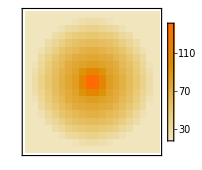
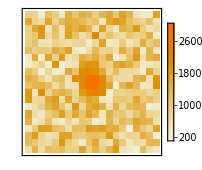

{{1},{{1},118,{{515.727,645.552,676.845,458.035,429.204,458.102,88,624.651,271.525,469.084,485.95,483.989,676.932},98,{1}}}}[1,1,1,1]
 |  |  |  |

```mathematica
Block[{img},
img = Row[{
MatrixPlot[frameSingleFluorophore,
FrameTicks-> None,
PlotRange->All,
PlotLegends->Automatic,
ImageSize->6cm],
MatrixPlot[nframeSingleFluorophore,
FrameTicks-> None,
PlotRange->All,
PlotLegends->Automatic,
ImageSize->6cm]
}];
Export[FileNameJoin[{thesisImages,"methods-simulations-before-after-noise.pdf"}], img];
img]
```